```mathematica
(*css zebrafinch model*)
ns := Na ba pa + Nn bn pn;
nh:= Na ba (1-pa) + Nn bn (1-pn);
NNa :=ns vs((1-lsO) vI z +lsO qO ) + nh vh((1-lhO) vI z +lhO qO );
NNn :=ns vs((1-lsO) vI (1-z)+lsO(1- qO) ) + nh vh((1-lhO) vI (1-z)+lhO(1- qO) );
qO := (1-u)(Na/(Na +Nn));
(*leave Q in matrix below different than one up above recursions*)
```

```mathematica
AA:=({{0, 0, ba pa, bn pn}, {0, 0, ba(1-pa), bn(1-pn)}, {vs((1-lsO) vI z +lsO Qh), vh((1-lhO) vI z +lhO Qh ), 0, 0}, {vs((1-lsO) vI (1-z)+lsO(1- Qh) ), vh((1-lhO) vI (1-z)+lhO(1- Qh) ), 0, 0}})
```

```mathematica
NN = FullSimplify[NNn + NNa];
```

```mathematica
FFa=FullSimplify[NNa/NN/.{Na->Fa N0,Nn->(1-Fa)N0}];
```

```mathematica
FFn=FullSimplify[NNn/NN/.{Na->Fa N0,Nn->(1-Fa)N0}];
```

```mathematica
Simplify[FFn+FFa]
```

1

```mathematica
(* identify Q-hat for common strategy*)
Fasols=Solve[FFa==Fa,Fa];
```

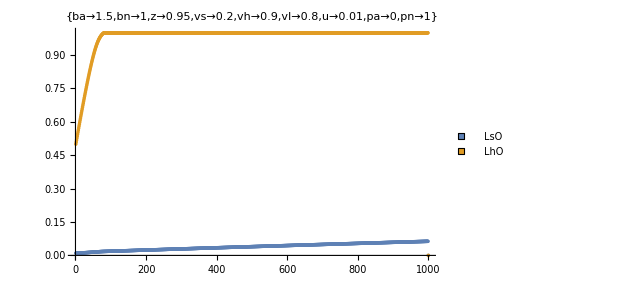

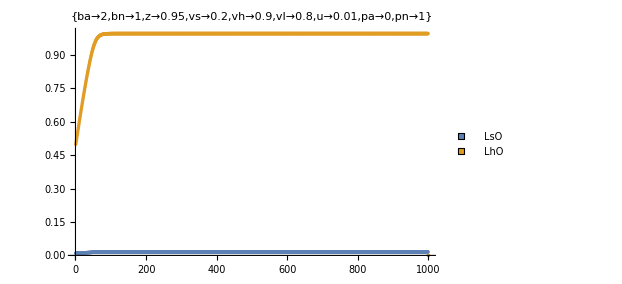

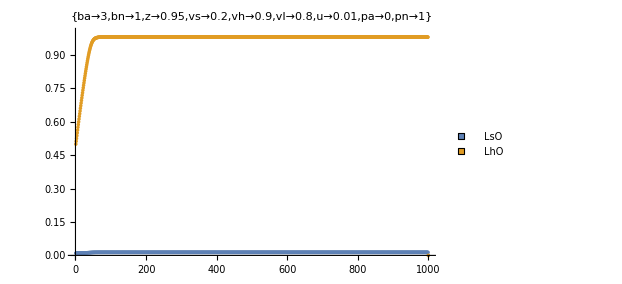

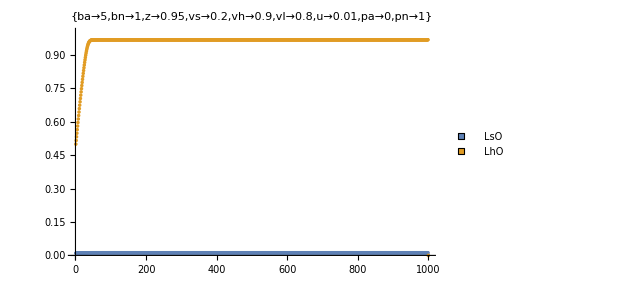

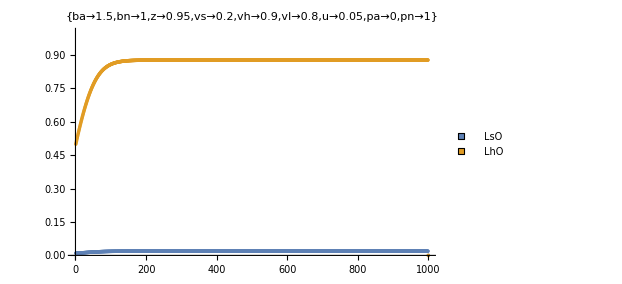

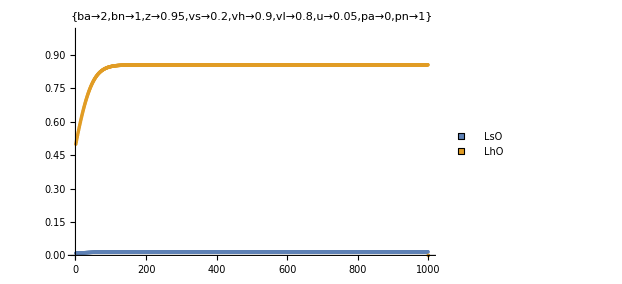

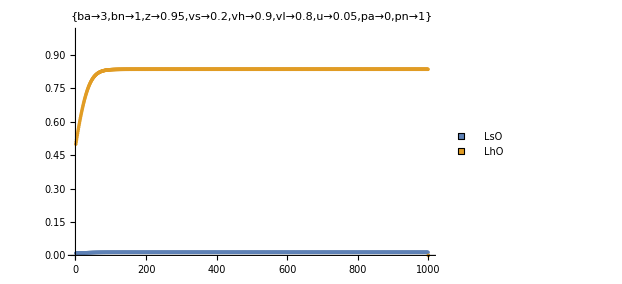

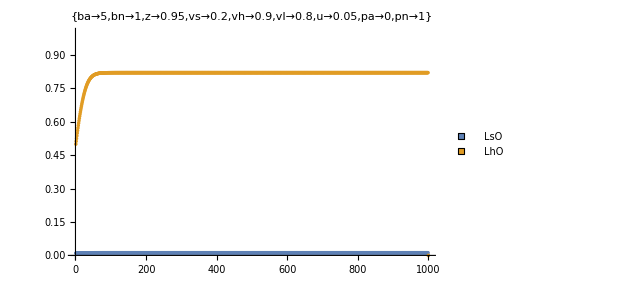

```mathematica
(* begin looping here*)
ulist={0.01,0.05,0.1, 0.2 , 0.4};
blist={1.5,2,3,5};
lsOstart=0.01;
lhOstart=0.5;
imax=1000;
For[h=1,h≤Length[ulist],h++,{
For[j=1,j≤Length[blist],j++,{
subs = {ba->blist[[j]],bn->1,z->.95,vs->.2,vh->.9,vI->.8  ,u->ulist[[h]] , pa -> 0, pn-> 1};
test = {lsO->0 ,lsV-> 0 ,lsI-> 0.8,lhO-> 0.8,lhI-> 0.2};
QHAT[LHO_,LSO_] :=Simplify[Fasols[[1,1,2]]/.{lhO->LHO,lhI -> LHI, lsO -> LSO, lsI-> LSI} /.subs];
(*isolate dominant eigenvalue*)
AA2=AA/.subs;
LL=Eigenvalues[AA2];
(*isolate Dominant eigenvalue, substitute in q-hat *)
Lambda1[ lsO_, lhO_,LHO_,LSO_]:= Simplify[LL[[2]]/.Qh->  QHAT[LHO,LSO]];
(*take partial derivatives to calculate gradient, substitute mutant for common type*)
DlsO=D[Lambda1[lsO, lhO,LHO,LSO],lsO]/. {LHO -> lhO,LSO-> lsO};
DlhO=D[Lambda1[lsO, lhO,LHO,LSO],lhO]/. {LHO -> lhO,LSO-> lsO};
(*try and graph*)
lsOtab=Table[0,{i,imax}];
lhOtab=Table[0,{i,imax}];
DlsOtab=Table[0,{i,imax}];
DlhOtab=Table[0,{i,imax}];
delta=0.08;
lsOtab[[1]]=lsOstart;
lhOtab[[1]]=lhOstart;
DlsOtab[[1]]=DlsO/.subs/.{lsO->lsOstart,lhO->lhOstart};
DlhOtab[[1]]=DlhO/.subs/.{lsO->lsOstart,lhO->lhOstart};
For[i=2,i<imax,i++,{

lsOtab[[i]]=lsOtab[[i-1]]  + delta DlsO/.subs/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lsOtab[[i]]=If[lsOtab[[i]]>1,1,lsOtab[[i]]];
lsOtab[[i]]=If[lsOtab[[i]]<0,0,lsOtab[[i]]];

lhOtab[[i]]=lhOtab[[i-1]]  + delta DlhO/.subs/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lhOtab[[i]]=If[lhOtab[[i]]>1,1,lhOtab[[i]]];
lhOtab[[i]]=If[lhOtab[[i]]<0,0,lhOtab[[i]]];

DlsOtab[[i]]=DlsO/.subs/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
DlhOtab[[i]]=DlhO/.subs/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
}];

Print[ListPlot[{lsOtab,lhOtab},PlotRange->{All,{0,1}},PlotLegends->PointLegend[{LsO,LhO},LegendMarkers->Graphics[Rectangle[]]],PlotLabel->subs, ImageSize->460]];
}]
}];
```

```mathematica
(* begin looping here, try matrices*)
PSTYLE={Directive[RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862]],Directive[RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961]],Directive[RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824]],Directive[RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961]],Directive[RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253]],Directive[RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],Dashed],Directive[RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961],Dashed],Directive[RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],Dashed],Directive[RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961],Dashed],Directive[RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253],Dashed]};
ulist={0.01,0.05,0.15, 0.25 , 0.5}
blist={1.5,2,3,5};
lsOstart=0.01;
lhOstart=0.5;
imax=1000;
lhOtab=lsOtab=Table[0,{i,imax-1}];
delta=0.1;
lsOtab[[1]]=lsOstart;
lhOtab[[1]]=lhOstart;
```

{0.01,0.05,0.15,0.25,0.5}

```mathematica
For[j=1,j≤Length[blist],j++,{
For[h=1,h≤Length[ulist],h++,{
subs = {ba->blist[[j]],bn->1,z->.6,vs->.7,vh->.9,vI->.8  ,u->ulist[[h]] , pa -> 0, pn-> 1};
test = {lsO->0 ,lsV-> 0 ,lsI-> 0.8,lhO-> 0.8,lhI-> 0.2};
QHAT[LHO_,LSO_] :=Simplify[Fasols[[1,1,2]]/.{lhO->LHO,lhI -> LHI, lsO -> LSO, lsI-> LSI} /.subs];
(*isolate dominant eigenvalue*)
AA2=AA/.subs;
LL=Eigenvalues[AA2];
(*isolate Dominant eigenvalue, substitute in q-hat *)
Lambda1[ lsO_, lhO_,LHO_,LSO_]:= Simplify[LL[[2]]/.Qh->  QHAT[LHO,LSO]];
(*take partial derivatives to calculate gradient, substitute mutant for common type*)
DlsO=D[Lambda1[lsO, lhO,LHO,LSO],lsO]/. {LHO -> lhO,LSO-> lsO};
DlhO=D[Lambda1[lsO, lhO,LHO,LSO],lhO]/. {LHO -> lhO,LSO-> lsO};
(*try and graph*)

For[i=2,i<imax,i++,{
lsOtab[[i]]=lsOtab[[i-1]]  + delta DlsO/.subs/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lsOtab[[i]]=If[lsOtab[[i]]>1,1,lsOtab[[i]]];
lsOtab[[i]]=If[lsOtab[[i]]<0,0,lsOtab[[i]]];

lhOtab[[i]]=lhOtab[[i-1]]  + delta DlhO/.subs/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lhOtab[[i]]=If[lhOtab[[i]]>1,1,lhOtab[[i]]];
lhOtab[[i]]=If[lhOtab[[i]]<0,0,lhOtab[[i]]];
}];
lsOtab1=If[h==1,lsOtab,lsOtab1];
lsOtab2=If[h==2,lsOtab,lsOtab2];
lsOtab3=If[h==3,lsOtab,lsOtab3];
lsOtab4=If[h==4,lsOtab,lsOtab4];
lsOtab5=If[h==5,lsOtab,lsOtab5];
lhOtab1=If[h==1,lhOtab,lhOtab1];
lhOtab2=If[h==2,lhOtab,lhOtab2];
lhOtab3=If[h==3,lhOtab,lhOtab3];
lhOtab4=If[h==4,lhOtab,lhOtab4];
lhOtab5=If[h==5,lhOtab,lhOtab5];
}];


Print[ListLinePlot[{lhOtab1,lhOtab2,lhOtab3,lhOtab4,lhOtab5, lsOtab1,lsOtab2,lsOtab3,lsOtab4,lsOtab5},PlotRange->{All,{0,1}},PlotStyle->PSTYLE,PlotLabels->ulist,AxesLabel->{time, freq of oblique},PlotLegends->{Placed[PointLegend[ulist],Bottom],Placed[LineLegend[{Normal,Dashed},{"healthy juv","stressed juv"}],Top]},PlotLabel->subs, ImageSize->460]];

Export["TestPDF03.pdf",%]

}];
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
lsOtab1
```

{0.01,0.0116724,0.01334,0.0150027,0.0166604,0.0183131,0.0199607,0.0216032,0.0232405,0.0248724,0.0264989,0.0281198,0.029735,0.0313443,0.0329476,0.0345447,0.0361353,0.0377192,0.0392962,0.0408658,0.0424277,0.0439815,0.0455267,0.0470628,0.0485891,0.050105,0.0516096,0.0531021,0.0545812,0.0560458,0.0574945,0.0589256,0.0603373,0.0617275,0.0630939,0.0644339,0.0657445,0.0670352,0.0683253,0.069615,0.0709042,0.0721929,0.0734811,0.0747688,0.076056,0.0773427,0.0786289,0.0799146,0.0811998,0.0824845,0.0837686,0.0850523,0.0863354,0.087618,0.0889001,0.0901817,0.0914628,0.0927433,0.0940234,0.0953029,0.0965819,0.0978604,0.0991383,0.100416,0.101693,0.102969,0.104245,0.10552,0.106795,0.108069,0.109343,0.110616,0.111889,0.113161,0.114432,0.115703,0.116974,0.118244,0.119513,0.120782,0.12205,0.123318,0.124585,0.125852,0.127118,0.128383,0.129648,0.130912,0.132176,0.13344,0.134702,0.135964,0.137226,0.138487,0.139747,0.141007,0.142267,0.143525,0.144783}

```mathematica
Append[lsOtab1,lsOtab2]
```

{0.01,0.0116724,0.01334,0.0150027,0.0166604,0.0183131,0.0199607,0.0216032,0.0232405,0.0248724,0.0264989,0.0281198,0.029735,0.0313443,0.0329476,0.0345447,0.0361353,0.0377192,0.0392962,0.0408658,0.0424277,0.0439815,0.0455267,0.0470628,0.0485891,0.050105,0.0516096,0.0531021,0.0545812,0.0560458,0.0574945,0.0589256,0.0603373,0.0617275,0.0630939,0.0644339,0.0657445,0.0670352,0.0683253,0.069615,0.0709042,0.0721929,0.0734811,0.0747688,0.076056,0.0773427,0.0786289,0.0799146,0.0811998,0.0824845,0.0837686,0.0850523,0.0863354,0.087618,0.0889001,0.0901817,0.0914628,0.0927433,0.0940234,0.0953029,0.0965819,0.0978604,0.0991383,0.100416,0.101693,0.102969,0.104245,0.10552,0.106795,0.108069,0.109343,0.110616,0.111889,0.113161,0.114432,0.115703,0.116974,0.118244,0.119513,0.120782,0.12205,0.123318,0.124585,0.125852,0.127118,0.128383,0.129648,0.130912,0.132176,0.13344,0.134702,0.135964,0.137226,0.138487,0.139747,0.141007,0.142267,0.143525,0.144783,{0.01,0.0114863,0.012961,0.0144239,0.0158748,0.0173135,0.0187398,0.0201533,0.0215538,0.022941,0.0243146,0.0256743,0.0270198,0.0283506,0.0296665,0.030967,0.0322518,0.0335204,0.0347725,0.0360076,0.0372253,0.0384251,0.0396067,0.0407696,0.0419133,0.0430374,0.0441416,0.0452253,0.0462883,0.04733,0.0483502,0.0493485,0.0503246,0.0512782,0.0522091,0.0531171,0.0540019,0.0548635,0.0557017,0.0565165,0.0573078,0.0580757,0.0588203,0.0595417,0.06024,0.0609154,0.0615682,0.0621986,0.0628069,0.0633934,0.0639586,0.0645027,0.0650263,0.0655298,0.0660136,0.0664782,0.0669241,0.0673519,0.0677619,0.0681547,0.0685309,0.068891,0.0692355,0.0695648,0.0698797,0.0701805,0.0704677,0.070742,0.0710037,0.0712533,0.0714914,0.0717184,0.0719346,0.0721407,0.072337,0.0725239,0.0727019,0.0728712,0.0730324,0.0731857,0.0733315,0.0734701,0.073602,0.0737273,0.0738464,0.0739596,0.0740671,0.0741693,0.0742664,0.0743585,0.0744461,0.0745292,0.0746081,0.074683,0.0747541,0.0748216,0.0748857,0.0749464,0.0750041}}